5.2×10^8-(5.2×10^8 κ Gamma[κ])/Gamma[1+κ]

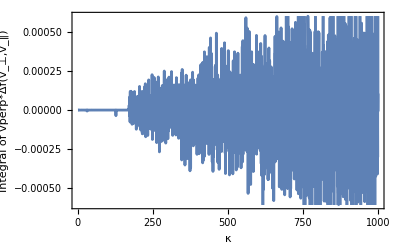

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
n=2000*0.26*10^6;
m=16*1.67*10^-27;
T=60*1.6*10^-19;
(*κ=10;*)
f1[vpar_,vperp_]:=(n (m/T)^(3/2))/(2 √2 π^(3/2))*Exp[-m*vpar^2/(2*T)]*Exp[-m*vperp^2/(2*T)];
f2[vpar_,vperp_,κ_]:=(m^(3/2) n)/(2 √2 π^(3/2)*T^(3/2))*(Exp[-m*vpar^2/(2*T)])*(1+(m*vperp^2)/(2*κ*T))^(-(κ+1));
(*
Plot[{f1[0,vperp],f2[0,vperp,10]},{vperp,0,100},Frame->True,FrameLabel->{"v_⊥(m/s)","f(v_⊥,v_‖)"}]

Manipulate[Plot[{f1[0,vperp],f2[0,vperp,κ]},{vperp,0,1000},Frame->True,FrameLabel->{"v_⊥(m/s)","f(v_⊥,v_‖)"}],{κ,2,100}]*)

Integrate[2*Pi*(f1[vpar,vperp] - f2[vpar,vperp,κ])*vperp,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->{κ>3/2}]

Plot[5.200000000000004*^8-(5.200000000000001*^8 κ Gamma[κ])/Gamma[1+κ],{κ,1.51,1000},Frame->True,FrameLabel->{"κ","Integral of vperp*Δf(v_⊥,v_‖)"}]
```

```mathematica
2000*0.26*10^6
```

5.2×10^8

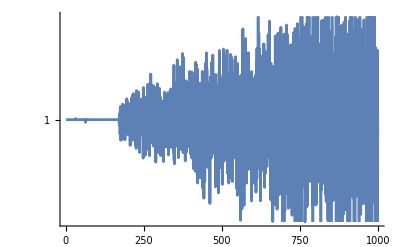

```mathematica
LogPlot[κ Gamma[κ]/Gamma[1+κ],{κ,1.51,1000}]
```

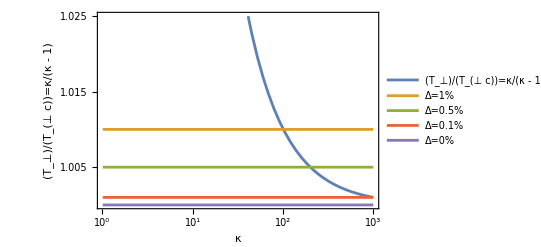

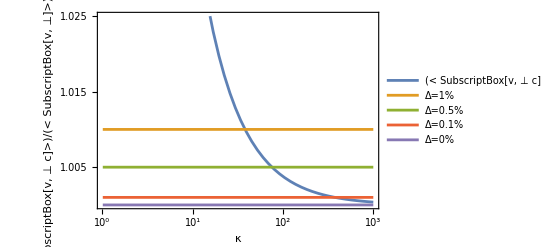

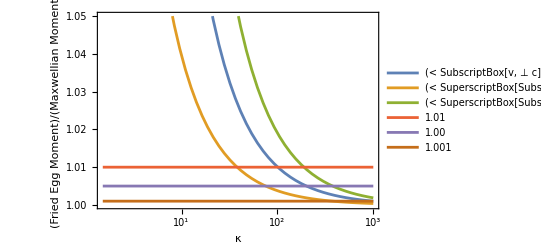

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Plot[{κ/(κ-1),1.01,1.005,1.001,1},{κ,1.01,1000},Frame->True,FrameLabel->{"κ","(T_⊥)/(T_(⊥ c))=κ/(κ - 1)"},PlotLegends->{"(T_⊥)/(T_(⊥ c))=κ/(κ - 1)","Δ=1%","Δ=0.5%","Δ=0.1%","Δ=0%"},ScalingFunctions->{"Log10","Linear"}]
Plot[{(√κ Gamma[-1/2+κ])/Gamma[κ],1.01,1.005,1.001,1},{κ,1.01,1000},Frame->True,FrameLabel->{"κ","(< SubscriptBox[v,  ⊥ c]>)/(< SubscriptBox[v, ⊥]>)=(√κ)/Γ[κ]"},PlotLegends->{"(< SubscriptBox[v,  ⊥ c]>)/(< SubscriptBox[v, ⊥]>)=(√κ)/Γ[κ]","Δ=1%","Δ=0.5%","Δ=0.1%","Δ=0%"},ScalingFunctions->{"Log10","Linear"}]
Plot[{κ/(κ-1),(√κ Gamma[-1/2+κ])/Gamma[κ],(κ^(3/2) Gamma[-3/2+κ])/Gamma[κ],1.01,1.005,1.001},{κ,1.51,1000},Frame->True,FrameLabel->{"κ","(Fried Egg Moment)/(Maxwellian Moment)"},PlotLegends->{"(< SubscriptBox[v,  ⊥ c]>)/(< SubscriptBox[v, ⊥]>)=(√κ)/Γ[κ]","(< SuperscriptBox[SubscriptBox[v,  ⊥ c], 2]>)/(< SuperscriptBox[SubscriptBox[v, ⊥], 2]>)=κ/(κ - 1)","(< SuperscriptBox[SubscriptBox[v,  ⊥ c], 3]>)/(< SuperscriptBox[SubscriptBox[v, ⊥], 3]>)=κ^(3/2)/Gamma[κ]","1.01","1.00","1.001"},ScalingFunctions->{"Log10","Linear"},FrameStyle->Directive[Bold,20],FrameTicksStyle->Black,PlotRange->{All,{1,1.05}}]
```

```mathematica
""
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Plot[{κ/(κ-1),1.01,1.005,1.001,1},{κ,1.51,1000},Frame->True,FrameLabel->{"κ","(T_⊥)/(T_(⊥ c))=κ/(κ - 1)"},PlotLegends->{"κ/(κ - 1)","Δ=1%","Δ=0.5%","Δ=0.1%","Δ=0%"},ScalingFunctions->{"Log10","Linear"}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={m>0,n>0,Tpar>0,Tperp>0,κ>1};
(*κ=10;*)
f1[vpar_,vperp_]:=(n (m)^(3/2))/(2 √2 π^(3/2)*Tperp*Sqrt[Tpar])*Exp[-m*vpar^2/(2*Tpar)]*Exp[-m*vperp^2/(2*Tperp)];
f2[vpar_,vperp_]:=(m^(3/2) n)/(2 √2 π^(3/2)*Tperp*Sqrt[Tpar])*(Exp[-m*vpar^2/(2*Tpar)])*(1+(m*vperp^2)/(2*κ*Tperp))^(-(κ+1));
Integrate[2*Pi*vperp*f1[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[2*Pi*vperp*f2[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]

Integrate[2*Pi*vperp^2*f1[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[2*Pi*vperp^2*f2[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[2*Pi*vperp*vpar*f1[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[2*Pi*vperp*vpar*f2[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[2*Pi*vperp^3*f1[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[2*Pi*vperp^3*f2[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[2*Pi*vperp*vpar^2*f1[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[2*Pi*vperp*vpar^2*f2[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[2*Pi*vperp^4*f1[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[2*Pi*vperp^4*f2[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[2*Pi*vperp*vpar^3*f1[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[2*Pi*vperp*vpar^3*f2[vpar,vperp],{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
```

n

n

n √(π/2) √(Tperp/m)

(n √(π/2) √((Tperp κ)/m) Gamma[-1/2+κ])/Gamma[κ]

0

0

(2 n Tperp)/m

(2 n Tperp κ)/(m (-1+κ))

(n Tpar)/m

(n Tpar)/m

3 n √(π/2) (Tperp/m)^(3/2)

ConditionalExpression[(3 m n √(π/2) ((Tperp κ)/m)^(5/2) Gamma[-3/2+κ])/(Tperp Gamma[1+κ]), κ>3/2]

0

0

```mathematica
FullSimplify[((n √(π/2) √((Tperp κ)/m) Gamma[-1/2+κ])/Gamma[κ])/(n √(π/2) √(Tperp/m)),assumps]
((2 n Tperp κ)/(m (-1+κ)))/((2 n Tperp)/m)
FullSimplify[((3 m n √(π/2) ((Tperp κ)/m)^(5/2) Gamma[-3/2+κ])/(Tperp Gamma[1+κ]))/(3 n √(π/2) (Tperp/m)^(3/2)),assumps]
```

(√κ Gamma[-1/2+κ])/Gamma[κ]

κ/(-1+κ)

(κ^(3/2) Gamma[-3/2+κ])/Gamma[κ]